## Classify

Classify generates a ClassifierFunction based on the classes and examples given. A ClassifierFunction represents a function generated by the Classify function. Classify and provide us with the probabilities of classes. It can work on variety of data types like numbers, images, sounds, colors etc. A number of ClassifierFucntions are built into Classify function. For e.g. “Language”, “Gender”, “Sentiment”, “NotablePerson” etc. It takes input as a list of rules, with further nesting. It works well with less data. 
Let’s start with a simple dataset.
Number of models that Classify supports.

Logistic Regression

Markov

NaiveBayes

NearestNeighbors

NeuralNetwork

RandomForest

SupportVectorMachine

```mathematica
dataset = Table[x->"A",{x,Range[10]}];
dataset2 = Table[x->"B",{x,Range[11,20,1]}];
dataset3 = Table[x->"C",{x,Range[21,30,1]}];
finalDataset = Join[dataset,dataset2,dataset3]
```

{1→A,2→A,3→A,4→A,5→A,6→A,7→A,8→A,9→A,10→A,11→B,12→B,13→B,14→B,15→B,16→B,17→B,18→B,19→B,20→B,21→C,22→C,23→C,24→C,25→C,26→C,27→C,28→C,29→C,30→C}

So now we have our dataset with 3 classes. Let’s try it on our Classify function

```mathematica
c = Classify[finalDataset]
```

ClassifierFunction[…]

```mathematica
c[21.5]
```

C

```mathematica
c[20.5]
```

C

```mathematica
c[20.4]
```

B

Let’s see the probabilities.

```mathematica
c[20.5, "Probabilities"]
```

<|A→1.1508×10^-77,B→0.496844,C→0.503156|>

B and C were close.

```mathematica
c[20.4,"Probabilities"]
```

<|A→1.15289×10^-76,B→0.852269,C→0.147731|>

Here the system is confident, its B.
Let’s try it on images of Dogs and Cats. I will be using a very small dataset of 10 images per class, since don’t have powerful computer.
Remember when specifying labels for data all at once, use associations.

```mathematica
CatsVsDogs = Classify[<|
"cat"-> {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
"dog"-> {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

ClassifierFunction[…]

```mathematica
CatsVsDogs[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}, "Probabilities"]
```

{<|cat→1.5388×10^-165,dog→1.|>,<|cat→1.,dog→3.14995×10^-129|>,<|cat→1.,dog→1.97169×10^-82|>,<|cat→1.,dog→4.04023×10^-113|>,<|cat→2.1212×10^-101,dog→1.|>,<|cat→2.09485×10^-181,dog→1.|>}

Getting some information about our model. For this we use ClassifierMeasurements. It takes the ClassifierFunction and the test data, to calculate the accuracy and stuff.

```mathematica
cm = ClassifierMeasurements[CatsVsDogs,{-Graphics-->"dog",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"dog"}]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

1.

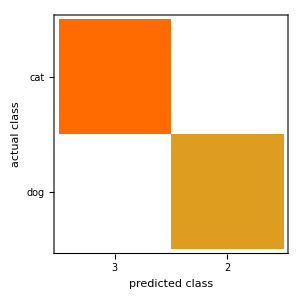

```mathematica
cm["ConfusionMatrixPlot"]
```

To get more information about the model itself, we use ClassifierInformation.

```mathematica
ClassifierInformation[CatsVsDogs]
```

Classifier information
Method | Logistic regression
Number of classes | 2
Number of features | 1
Number of training examples | 20
L1 regularization coefficient | 0
L2 regularization coefficient | 1.×10^-10

```mathematica
ClassifierInformation[CatsVsDogs,"Classes"]
```

{cat,dog}

```mathematica
ClassifierInformation[CatsVsDogs,"TrainingTime"]
```

4.11778 s

```mathematica
ClassifierInformation[CatsVsDogs,FeatureTypes] (* what is the type of the input that this classifier takes*)
```

<|f1→Image|>

Now let’s try some in-built ClassifierFunctions. Be sure to put functions in front.

```mathematica
Classify["CountryFlag",Entity["Country","India"]["FlagImage"]]
```

MachineLearning`Models`ClassifierCountryFlag`Private`h5dread[MachineLearning`Models`ClassifierCountryFlag`Private`h5dopen[MachineLearning`Models`ClassifierCountryFlag`Private`h5fopen[/Users/khushmeetsingh/Library/Mathematica/Paclets/Repository/Classifier_CountryFlag-0.9.7/Model.wmlf,MachineLearning`Models`ClassifierCountryFlag`Private`H5FACCRDWR],ExpressionSkeleton,MachineLearning`Models`ClassifierCountryFlag`Private`H5PDEFAULT],MachineLearning`Models`ClassifierCountryFlag`Private`H5TMSTRING,MachineLearning`Models`ClassifierCountryFlag`Private`H5SALL,MachineLearning`Models`ClassifierCountryFlag`Private`H5SALL,MachineLearning`Models`ClassifierCountryFlag`Private`H5PDEFAULT][-Graphics-,PerformanceGoal→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,BatchProcessing→Automatic,ClassPriors→Automatic,TieBreakerFunction→RandomChoice]

```mathematica
Classify["NotablePerson",Entity["Person","AlbertEinstein::6tb7g"][EntityProperty["Person","Image"]]]
```

Charles Dickens

```mathematica
Classify["ProgrammingLanguage","int main(){printf(\"hello world\");}"]
```

AWK

```mathematica
Classify["Sentiment","the gorgeously elaborate continuation of \" the lord of the rings \" trilogy is so huge that a column of words cannot adequately describe co-writer/director peter jackson's expanded vision of j . r . r . tolkien's middle-earth . "]
```

Neutral